```mathematica
Q[bj_,bh_]:=√(E^(2*bj)*Cosh[bh]^2-2Sinh[2bj]);
lp[bj_,bh_]:=E^bj Cosh[bh]+Q[bj,bh];
lm[bj_,bh_]:=E^bj Cosh[bh]-Q[bj,bh];
Zobc[bj_,bh_,n_]:=lp[bj,bh]^(n-1)*((E^bj Sinh[bh]^2)/Q[bj,bh]+1/(E^bj Q[bj,bh])+Cosh[bh])-lm[bj,bh]^(n-1)*((E^bj Sinh[bh]^2)/Q[bj,bh]+1/(E^bj Q[bj,bh])-Cosh[bh]);
Zpbc[bj_,bh_,n_]:=lp[bj,bh]^n+lm[bj,bh]^n
```

```mathematica
m2=D[Zobc[bj,bh,n],{bh,2}]/(Zobc[bj,bh,n]*n^2) /.{bh->0,bj->1/2.269}
m4=D[Zobc[bj,bh,n],{bh,4}]/(Zobc[bj,bh,n]*n^4)/.{bh->0, bj->1/2.269}
```

(0.+2.00049 0.910259^(-1+n)-0.000491583 2.1974^(-1+n)+1.11022×10^-16 (0.-2.19772 0.910259^(-2+n) (-1+n))+2. (0.+5.30538 2.1974^(-2+n) (-1+n)))/((1.11022×10^-16 0.910259^(-1+n)+2. 2.1974^(-1+n)) n^2)

1/((1.11022×10^-16 0.910259^(-1+n)+2. 2.1974^(-1+n)) n^4)(0.-131.932 0.910259^(-1+n)+133.932 2.1974^(-1+n)+12.0029 (0.-2.19772 0.910259^(-2+n) (-1+n))-0.0029495 (0.+5.30538 2.1974^(-2+n) (-1+n))+1.11022×10^-16 (0.+52.1539 0.910259^(-2+n) (-1+n)+14.4899 0.910259^(-3+n) (-2+n) (-1+n))+2. (0.-49.0463 2.1974^(-2+n) (-1+n)+84.4411 2.1974^(-3+n) (-2+n) (-1+n)))

```mathematica
N[1-m4/(3*m2^2)/.{n->50}]
```

0.0448609

```mathematica
N[1-m4/(3*m2^2)/.{n->100}]
```

0.0226025

```mathematica
N[1-m4/(3*m2^2)/.{n->200}]
```

0.0113421

```mathematica
N[1-m4/(3*m2^2)/.{n->400}]
```

0.00568103

```mathematica
m4
```

0.-131.932 0.910259^(-1+n)+133.932 2.1974^(-1+n)+12.0029 (0.-2.19772 0.910259^(-2+n) (-1+n))-0.0029495 (0.+5.30538 2.1974^(-2+n) (-1+n))+1.11022×10^-16 (0.+52.1539 0.910259^(-2+n) (-1+n)+14.4899 0.910259^(-3+n) (-2+n) (-1+n))+2. (0.-49.0463 2.1974^(-2+n) (-1+n)+84.4411 2.1974^(-3+n) (-2+n) (-1+n))

```mathematica
m2=D[Zpbc[bj,bh,n],{bh,2}]/(Zobc[bj,bh,n]*n^2) /.{bh->0,bj->1/2.269}
m4=D[Zpbc[bj,bh,n],{bh,4}]/(Zobc[bj,bh,n]*n^4) /.{bh->0, bj->1/2.269}
```

(0.-2.19772 0.910259^(-1+n) n+5.30538 2.1974^(-1+n) n)/((1.11022×10^-16 0.910259^(-1+n)+2. 2.1974^(-1+n)) n^2)

(0.+52.1539 0.910259^(-1+n) n-49.0463 2.1974^(-1+n) n+14.4899 0.910259^(-2+n) (-1+n) n+84.4411 2.1974^(-2+n) (-1+n) n)/((1.11022×10^-16 0.910259^(-1+n)+2. 2.1974^(-1+n)) n^4)

```mathematica
N[1-m4/(3 m2^2)/.{n->50}]
```

0.131271

```mathematica
N[1-m4/(3 m2^2)/.{n->100}]
```

0.110552

```mathematica
N[1-m4/(3 m2^2)/.{n->200}]
```

0.100193

```mathematica
N[1-m4/(3 m2^2)/.{n->400}]
```

0.0950134

General::munfl: (8.85956×10^-297)/562434001936 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.03184×10^-297)/565036352721 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.83482×10^-297)/567647723776 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

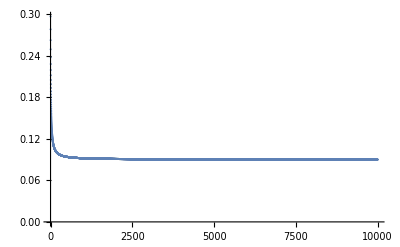

```mathematica
ListPlot[Table[1-m4/(3*m2^2),{n,10,10000,1}],PlotRange->Full]
```

```mathematica
n=10000000
1-m4/(3*m2^2)
```

10000000

General::munfl: 0.910259^9999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.910259^9999998 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.089834055692997

Если рассмотреть периодический случай сразу с учетом термодинамического предела (n→∞), то статсумма примет вид k*(λ_+)^n, где k = (1 + (lm/lp)^n)  = [1,2]

```mathematica
F[bj_,bh_,n_]:=2*lp[bj,bh]^n
```

```mathematica
m2=D[F[bj,bh,n],{bh,2}]/(F[bj,bh,n]*n^2) /.{bh->0};
m4=D[F[bj,bh,n],{bh,4}]/(F[bj,bh,n]*n^4)/.{bh->0};
```

```mathematica
N[1-m4/(3*m2^2)/.{n->400}]
```

0.00569082

Таким образом, кумулянт стремится к нулю

```mathematica
1-m4/(3*m2^2)
```

1-((3 (-1+n) n (ⅇ^bj+ⅇ^(2 bj)/(√(ⅇ^(2 bj)-2 Sinh[2 bj])))^2 (ⅇ^bj+√(ⅇ^(2 bj)-2 Sinh[2 bj]))^(-2+n)+n (ⅇ^bj-(3 ⅇ^(4 bj))/((ⅇ^(2 bj)-2 Sinh[2 bj])^(3/2))+(4 ⅇ^(2 bj))/(√(ⅇ^(2 bj)-2 Sinh[2 bj]))) (ⅇ^bj+√(ⅇ^(2 bj)-2 Sinh[2 bj]))^(-1+n)) (ⅇ^bj+√(ⅇ^(2 bj)-2 Sinh[2 bj]))^(2-n))/(3 n^2 (ⅇ^bj+ⅇ^(2 bj)/(√(ⅇ^(2 bj)-2 Sinh[2 bj])))^2)